```mathematica
ClearAll["Global`*"]
```

# Master Peoject Notebook

## Dirac Basis

## Preparation to calculate Bogoliubov coefficients

## Matrices Definition

```mathematica
σ= {{{1,0},{0,1}},{{0,1},{1,0}},{{0,-I},{I,0}},{{1,0},{0,-1}}};
σto={{{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}},{{0, 0, 1, 0}, {0, 0, 0, 1}, {1, 0, 0, 0}, {0, 1, 0, 0}},{{0, 0, -I, 0}, {0, 0, 0, -I}, {I, 0, 0, 0}, {0, I, 0, 0}},{{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}}};

otτ={{{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}},{{0, 1, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}},{{0, -I, 0, 0}, {I, 0, 0, 0}, {0, 0, 0, -I}, {0, 0, I, 0}},{{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, -1}}};
τ = {ArrayFlatten[{{otτ[[1]],0},{0,otτ[[1]]}}],ArrayFlatten[{{otτ[[2]],0},{0,otτ[[2]]}}],ArrayFlatten[{{otτ[[3]],0},{0,otτ[[3]]}}],ArrayFlatten[{{otτ[[4]],0},{0,otτ[[4]]}}]};
{τ[[1]]//MatrixForm,τ[[2]]//MatrixForm,τ[[3]]//MatrixForm,τ[[4]]//MatrixForm};
γD = {ArrayFlatten[{{σto[[1]],0},{0,-σto[[1]]}}],ArrayFlatten[{{0,σto[[2]]},{-σto[[2]],0}}],ArrayFlatten[{{0,σto[[3]]},{-σto[[3]],0}}],ArrayFlatten[{{0,σto[[4]]},{-σto[[4]],0}}]};
{γD[[1]]//MatrixForm,γD[[2]]//MatrixForm,γD[[3]]//MatrixForm,γD[[4]]//MatrixForm};
```

## Finding EigenValues[] and EigenVectors[]

```mathematica
DiracHamiltonianD=-M[η]*γD[[1]]-γD[[1]].γD[[4]]*k+f[η]/2(Sum[γD[[1]].γD[[i]].τ[[i]],{i,2,4}]);
AnsD=FullSimplify[Eigensystem[-M[η]*γD[[1]]-γD[[1]].γD[[4]]*k+f[η]/2(Sum[γD[[1]].γD[[i]].τ[[i]],{i,2,4}])]];
ωD = Table[AnsD[[1]][[i]],{i,1,8}];
uD = Table[AnsD[[2]][[i]],{i,1,8}];
```

```mathematica
fωD[η_,k_]:={-1/2 √((-2 k+f[η])^2+4 M[η]^2),1/2 √((-2 k+f[η])^2+4 M[η]^2),-1/2 √((2 k+f[η])^2+4 M[η]^2),1/2 √((2 k+f[η])^2+4 M[η]^2),-1/2 √(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2)),1/2 √(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2)),-1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)),1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2))}
```

### Simplifying EigenVectors

```mathematica
suD=Table[0,{i,1,8}];
```

```mathematica
suD[[1]]=uD[[1]];
suD[[1]]=Simplify[uD[[1]]/.√((-2 k+f[η])^2+4 M[η]^2)->2ω1 ];
suD[[1]]=√(ω1-M[η])suD[[1]]/. (2 k-f[η])->2*Sign[2 k-f[η]]*√(ω1^2-M[η]^2);
suD[[1]]=suD[[1]]/.(√(ω1-M[η])(ω1+M[η]))/(√(ω1^2-M[η]^2))->√(ω1+M[η]);
```

```mathematica
suD[[2]]=Simplify[uD[[2]]/.√((-2 k+f[η])^2+4 M[η]^2)->2ω1 ];
suD[[2]]=√(ω1+M[η])suD[[2]]/. (2 k-f[η])->2*Sign[2 k-f[η]]*√(ω1^2-M[η]^2);
suD[[2]]=suD[[2]]/.((ω1-M[η])√(ω1+M[η]))/(√(ω1^2-M[η]^2))->√(ω1-M[η]);
```

```mathematica
suD[[3]]=Simplify[uD[[3]]/.√((2 k+f[η])^2+4 M[η]^2)->2ω2 ];
suD[[3]]=√(ω2-M[η])suD[[3]]/. (2 k+f[η])->2*Sign[2 k+f[η]]*√(ω2^2-M[η]^2);
suD[[3]]=suD[[3]]/.(√(ω2-M[η])(ω2+M[η]))/(√(ω2^2-M[η]^2))->√(ω2+M[η]);
```

```mathematica
suD[[4]]=Simplify[uD[[4]]/.√((2 k+f[η])^2+4 M[η]^2)->2ω2 ];
suD[[4]]=√(ω2+M[η])suD[[4]]/. (2 k+f[η])->2*Sign[2 k+f[η]]*√(ω2^2-M[η]^2);
suD[[4]]=suD[[4]]/.((ω2-M[η])√(ω2+M[η]))/(√(ω2^2-M[η]^2))->√(ω2-M[η]);
```

```mathematica
suD[[5]]=Simplify[uD[[5]]/.√(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))->2ω3 ];
suD[[5]]=√(ω3-M[η])suD[[5]]/.√(ω3-M[η]) (ω3+M[η])->√(ω3^2-M[η]^2)√(ω3+M[η]);
suD[[5]]=suD[[5]]/.√(ω3^2-M[η]^2)->√(5/4 f[η]^2+k^2-√(f[η]^2 (k^2+f[η]^2)));
suD[[5]]=Simplify[suD[[5]]/.k^2+(5 f[η]^2)/4-√(f[η]^2 (k^2+f[η]^2)) -> (√(k^2+f[η]^2)-(√(f[η]^2))/2)^2];
suD[[5]]=√(1/2 √(f[η]^2)+√(k^2+f[η]^2))*suD[[5]]/.√(1/2 √(f[η]^2)+√(k^2+f[η]^2))√((-1/2 √(f[η]^2)+√(k^2+f[η]^2))^2) ->√(k^2+3/4 f[η]^2)√(-1/2 √(f[η]^2)+√(k^2+f[η]^2));
suD[[5]]=√(k f[η]+√(f[η]^2 (k^2+f[η]^2)))*suD[[5]]/.√(k f[η]+√(f[η]^2 (k^2+f[η]^2)))(-k f[η]+√(f[η]^2 (k^2+f[η]^2)))->f[η]^2 √(-k f[η]+√(f[η]^2 (k^2+f[η]^2)));

suD[[5]]=suD[[5]]/.(2 f[η]^2)/(f[η]^3-2 f[η] √(f[η]^2 (k^2+f[η]^2)))->(2 f[η])/(f[η]^2-2  √(f[η]^2 (k^2+f[η]^2)));
suD[[5]]=suD[[5]]/.(2 f[η])/(f[η]2-2  √(f[η]^2 (k^2+f[η]^2)))->(-2 f[η])/(-f[η]^2+2  √(f[η]^2 (k^2+f[η]^2)));
suD[[5]]=1/(√(f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))))suD[[5]]/.2/((f[η]^2-2 √(f[η]^2 (k^2+f[η]^2))) √(f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))))->-2/(2*√(f[η]^2 k^2+3/4 f[η]^4)√(-f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))));
suD[[5]] = suD[[5]]/.f[η] √(k^2+(3 f[η]^2)/4)->√(k^2 f[η]^2+(3 f[η]^4)/4);
```

```mathematica
suD[[6]]=Simplify[uD[[6]]/.√(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))->2ω3 ];
suD[[6]]=√(ω3+M[η])suD[[6]]/.√(ω3+M[η]) (ω3-M[η])->√(ω3^2-M[η]^2)√(ω3-M[η]);
suD[[6]]=suD[[6]]/.√(ω3^2-M[η]^2)->√(5/4 f[η]^2+k^2-√(f[η]^2 (k^2+f[η]^2)));
suD[[6]]=Simplify[suD[[6]]/.k^2+(5 f[η]^2)/4-√(f[η]^2 (k^2+f[η]^2)) -> (√(k^2+f[η]^2)-(√(f[η]^2))/2)^2];
suD[[6]]=√(1/2 √(f[η]^2)+√(k^2+f[η]^2))*suD[[6]]/.√((-1/2 √(f[η]^2)+√(k^2+f[η]^2))^2) √(1/2 √(f[η]^2)+√(k^2+f[η]^2))->√(k^2+3/4 f[η]^2)√(-1/2 √(f[η]^2)+√(k^2+f[η]^2));
suD[[6]]=suD[[6]]/.(2(k f[η]-√(f[η]^2 (k^2+f[η]^2)))) ->-2(-k f[η]+√(f[η]^2 (k^2+f[η]^2))) ;
suD[[6]]=√(k f[η]+√(f[η]^2 (k^2+f[η]^2)))*suD[[6]]/.√(k f[η]+√(f[η]^2 (k^2+f[η]^2)))(-k f[η]+√(f[η]^2 (k^2+f[η]^2)))->f[η]^2 √(-k f[η]+√(f[η]^2 (k^2+f[η]^2)));
suD[[6]]=suD[[6]]/.(-2*f[η]^2)/(f[η]^3-2 f[η] √(f[η]^2 (k^2+f[η]^2)))->(-2* f[η])/(f[η]^2-2  √(f[η]^2 (k^2+f[η]^2)));
suD[[6]]=suD[[6]]/.(-2*f[η]^2)/(f[η]^3-2 f[η] √(f[η]^2 (k^2+f[η]^2)))->(2* f[η])/(-f[η]^2+2  √(f[η]^2 (k^2+f[η]^2)));
suD[[6]]=1/(√(f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))))suD[[6]]/.-2/((f[η]^2-2 √(f[η]^2 (k^2+f[η]^2))) √(f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))))->2/(2 √(f[η]^2 k^2+3/4 f[η]^4)√(-f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))));
suD[[6]] = suD[[6]]/.f[η] √(k^2+(3 f[η]^2)/4)->√(k^2 f[η]^2+(3 f[η]^4)/4);
```

```mathematica
suD[[7]]=Simplify[uD[[7]]/. √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2))->2ω4 ];
suD[[7]]=√(ω4-M[η])suD[[7]]/.√(ω4-M[η]) (ω4+M[η])->√(ω4^2-M[η]^2)√(ω4+M[η]);
suD[[7]]=suD[[7]]/.√(ω4^2-M[η]^2)->√(5/4 f[η]^2+k^2+√(f[η]^2 (k^2+f[η]^2)));
suD[[7]]=Simplify[suD[[7]]/.k^2+(5 f[η]^2)/4+√(f[η]^2 (k^2+f[η]^2)) -> (√(k^2+f[η]^2)+(√(f[η]^2))/2)^2];
suD[[7]]=√(-1/2 √(f[η]^2)+√(k^2+f[η]^2))*suD[[7]]/.√(-1/2 √(f[η]^2)+√(k^2+f[η]^2))√((1/2 √(f[η]^2)+√(k^2+f[η]^2))^2) ->√(k^2+3/4 f[η]^2)√(1/2 √(f[η]^2)+√(k^2+f[η]^2));
suD[[7]]=√(-k f[η]+√(f[η]^2 (k^2+f[η]^2)))*suD[[7]]/.√(-k f[η]+√(f[η]^2 (k^2+f[η]^2)))(k f[η]+√(f[η]^2 (k^2+f[η]^2)))->f[η]^2 √(k f[η]+√(f[η]^2 (k^2+f[η]^2)));
suD[[7]]=suD[[7]]/.(-2 f[η]^2)/(f[η]^3+2 f[η] √(f[η]^2 (k^2+f[η]^2)))->(-2 f[η])/(f[η]^2+2  √(f[η]^2 (k^2+f[η]^2)));
suD[[7]]=1/(√(-f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))))suD[[7]]/.1/(√(-f[η]^2+2 √(f[η]^2 (k^2+f[η]^2)))(f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))))->1/(2*√(f[η]^2 k^2+3/4 f[η]^4)√(f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))));
suD[[7]] = suD[[7]]/.f[η] √(k^2+(3 f[η]^2)/4)->√(k^2 f[η]^2+(3 f[η]^4)/4);
```

```mathematica
suD[[8]]=Simplify[uD[[8]]/. √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2))->2ω4 ];
suD[[8]]=√(ω4+M[η])suD[[8]]/.√(ω4+M[η]) (ω4-M[η])->√(ω4^2-M[η]^2)√(ω4-M[η]);
suD[[8]]=suD[[8]]/.√(ω4^2-M[η]^2)->√(5/4 f[η]^2+k^2+√(f[η]^2 (k^2+f[η]^2)));
suD[[8]]=Simplify[suD[[8]]/.k^2+(5 f[η]^2)/4+√(f[η]^2 (k^2+f[η]^2)) -> (√(k^2+f[η]^2)+(√(f[η]^2))/2)^2];
suD[[8]]=√(-1/2 √(f[η]^2)+√(k^2+f[η]^2))*suD[[8]]/.√(-1/2 √(f[η]^2)+√(k^2+f[η]^2))√((1/2 √(f[η]^2)+√(k^2+f[η]^2))^2) ->√(k^2+3/4 f[η]^2)√(1/2 √(f[η]^2)+√(k^2+f[η]^2));
suD[[8]]=√(-k f[η]+√(f[η]^2 (k^2+f[η]^2)))*suD[[8]]/.√(-k f[η]+√(f[η]^2 (k^2+f[η]^2)))(k f[η]+√(f[η]^2 (k^2+f[η]^2)))->f[η]^2 √(k f[η]+√(f[η]^2 (k^2+f[η]^2)));
suD[[8]]=suD[[8]]/.(2 f[η]^2)/(f[η]^3+2 f[η] √(f[η]^2 (k^2+f[η]^2)))->(2 f[η])/(f[η]^2+2  √(f[η]^2 (k^2+f[η]^2)));
suD[[8]]=1/(√(-f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))))suD[[8]]/.1/(√(-f[η]^2+2 √(f[η]^2 (k^2+f[η]^2)))(f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))))->1/(2*√(f[η]^2 k^2+3/4 f[η]^4)√(f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))));
suD[[8]] = suD[[8]]/.f[η] √(k^2+(3 f[η]^2)/4)->√(k^2 f[η]^2+(3 f[η]^4)/4);
```

```mathematica
nsuD = suD;
nsuD[[1]] = 1/(√(2*ω1))*nsuD[[1]];
nsuD[[2]]= 1/(√(2*ω1))*nsuD[[2]];
nsuD[[3]] = 1/(√(2*ω2))*nsuD[[3]];
nsuD[[4]] = 1/(√(2*ω2))*nsuD[[4]];
nsuD[[5]]=1/(√(2*ω3*√(k^2+f[η]^2)))*nsuD[[5]];
nsuD[[6]]=1/(√(2*ω3*√(k^2+f[η]^2)))*nsuD[[6]];
nsuD[[7]]=1/(√(2*ω4*√(k^2+f[η]^2)))*nsuD[[7]];
nsuD[[8]]=1/(√(2*ω4*√(k^2+f[η]^2)))*nsuD[[8]];
```

### Check that simplifying went correct

```mathematica
(* check scalar product *)
errors =0;
For[i=1,i<=8,i++,
 For[j=1,j<=i,j++,
  product = Assuming[k>0&&f[η]>0,FullSimplify[Dot[nsuD[[i]],nsuD[[j]]]]];
  product=product/.Sign[2 k-f[η]]^2->1;
  product=product/.Sign[2 k+f[η]]^2->1;
  product=product/.√(ω3-M[η]) √(ω3+M[η])->√(5/4 f[η]^2+k^2-√(f[η]^2 (k^2+f[η]^2)));
  product=product/.√(f[η]^2) (k^2+f[η]^2)-√(k^2+f[η]^2) √(f[η]^2 (k^2+f[η]^2))->0;
  product=product/.√(ω4-M[η]) √(ω4+M[η])->√(5/4 f[η]^2+k^2+√(f[η]^2 (k^2+f[η]^2)));
  product=product/.-f[η]^2 √(k^2+f[η]^2)+√(f[η]^2) √(f[η]^2 (k^2+f[η]^2))->0;
  product=product/.ω3->1/2 √(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2));
  product=product/.ω4->1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2));
  product=product/.√(-2 M[η]+√(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))) √(-M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)))->√2(-M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)));
         product=Simplify[product/.√(2 M[η]+√(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))) √(M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)))->√2(M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)))];       
  product=product/.k f[η]-√(f[η]^2 (k^2+f[η]^2))+√(-k f[η]+√(f[η]^2 (k^2+f[η]^2))) √(k f[η]+√(f[η]^2 (k^2+f[η]^2)))->0;
         
If[i==j && (product===0) , errors++; Print[i,j, product]];  
  If[i!=j && !(product===0) , errors++;Print[i,j,product]];
]
]
If[errors==0,Print[True];];
If[errors!=0,Print[False];];
```

True

```mathematica
Table[ Assuming[k>0&&f[η]>0,FullSimplify[Dot[nsuD[[i]],nsuD[[j]]]]],{i,1,8},{j,1,8}];
```

```mathematica
(* check that suD are proportional to uD*)
errors = 0;
For[i=1, i<=8, i++,
	multiplier=0;
	For[j=1,j<=8,j++,
		If[uD[[i]][[j]]===1,
			multiplier = suD[[i]][[j]];
		];
	];
	muD = multiplier* uD[[i]];
	For[j=1,j<=8,j++,
		If[suD[[i]][[j]]===0 && muD[[j]] != 0,
			Print["Error for: ",i,j];
			errors += 1;
		];
		If[!suD[[i]][[j]]===0,
			If[! Assuming[f[η]>0 && k >0&&M[η]>0,FullSimplify[muD[[j]]/suD[[i]][[j]]==1]],
				Print["Error for: ",i,j, "got:",Assuming[f[η]>0 && k >0&&M[η]>0,FullSimplify[muD[[j]]/suD[[i]][[j]]]], muD[[j]], uD[[i]][[j]]];
				errors+=1;
			];
		];
	]
]
If[errors == 0, Print[True],Print[False]]
```

True

## derivatives of eigenvectors, products of eigenvectors derivatives and eigenvectors

```mathematica
dnsuD= Table[D[nsuD[[i]],η],{i,1,8}];
```

### scalar product of eigenvectors and its derivatives

```mathematica
productsD=Table[Dot[nsuD[[i]],dnsuD[[j]]],{i,1,8},{j,1,8}];
productsD//MatrixForm;
```

```mathematica
productsD==Assuming[f[η]>0 && k >0&&M[η]>0, FullSimplify[productsD]];
```

### check that up and down do not mix

```mathematica
errors =0;
For[i=3,i<=4,i++,
  For[j=1,j<=2,j++,
    If[!(productsD[[i]][[j]]==0) , errors++];  
  ]
]
For[i=1,i<=2,i++,
  For[j=3,j<=4,j++,
    If[!(productsD[[i]][[j]]==0) , errors++];  
  ]
]
For[i=5,i<=8,i++,
  For[j=1,j<=4,j++,
    If[!(productsD[[i]][[j]]==0) , errors++];  
  ]
]
For[i=1,i<=4,i++,
  For[j=5,j<=8,j++,
    If[!(productsD[[i]][[j]]==0) , errors++];  
  ]
]
If[errors ==0, Print[True]]
```

True

```mathematica
productsD1 = Table[FullSimplify[productsD[[i]][[j]]],{i,1,2},{j,1,2}];
```

```mathematica
productsD2 = Table[FullSimplify[productsD[[i]][[j]]],{i,3,4},{j,3,4}];
```

```mathematica
productsD3 = Table[FullSimplify[productsD[[i]][[j]]],{i,5,8},{j,5,8}];
```

#### Mixing of aup-up (assumption: Sign'[2 k-f[η]]->0)

```mathematica
sproductsD1 =Assuming[k>0&& M[η]>0&&ω1 > M[η]&&f[η]>0 && 2k!=f[η],FullSimplify[productsD1/.1/Sign[2 k-f[η]]^2->1/.Sign[2 k-f[η]]^2->1/.Sign'[2 k-f[η]]->0]]
```

{{0,M'[η]/(2 √(ω1^2-M[η]^2))},{-M'[η]/(2 √(ω1^2-M[η]^2)),0}}

#### Mixing of adown-down(assumption: Sign'[2 k-f[η]]->0)

```mathematica
sproductsD2 =FullSimplify[Assuming[k>0&& M[η]>0&&ω2 > M[η]&&f[η]>0,FullSimplify[productsD2/.1/Sign[2 k-f[η]]^2->1/.Sign[2 k-f[η]]^2->1/.Sign'[2 k-f[η]]->0]]/.Sign'[2 k+f[η]]->0]
```

{{0,M'[η]/(2 √(ω2^2-M[η]^2))},{-M'[η]/(2 √(ω2^2-M[η]^2)),0}}

### Mixed part

```mathematica
sproductsD3=Assuming[k>0&& M[η]>0&&ω1 > M[η]&&f[η]>0,FullSimplify[productsD3]]
```

{{0,M'[η]/(2 √(ω3-M[η]) √(ω3+M[η])),(k (√(ω3-M[η]) √(ω4-M[η])-√(ω3+M[η]) √(ω4+M[η])) f'[η])/(4 √ω3 √ω4 (k^2+f[η]^2)),(k (√(ω4-M[η]) √(ω3+M[η])+√(ω3-M[η]) √(ω4+M[η])) f'[η])/(4 √ω3 √ω4 (k^2+f[η]^2))},{-M'[η]/(2 √(ω3-M[η]) √(ω3+M[η])),0,(k (√(ω4-M[η]) √(ω3+M[η])+√(ω3-M[η]) √(ω4+M[η])) f'[η])/(4 √ω3 √ω4 (k^2+f[η]^2)),(k (-√(ω3-M[η]) √(ω4-M[η])+√(ω3+M[η]) √(ω4+M[η])) f'[η])/(4 √ω3 √ω4 (k^2+f[η]^2))},{(k (-√(ω3-M[η]) √(ω4-M[η])+√(ω3+M[η]) √(ω4+M[η])) f'[η])/(4 √ω3 √ω4 (k^2+f[η]^2)),-(k (√(ω4-M[η]) √(ω3+M[η])+√(ω3-M[η]) √(ω4+M[η])) f'[η])/(4 √ω3 √ω4 (k^2+f[η]^2)),0,M'[η]/(2 √(ω4-M[η]) √(ω4+M[η]))},{-(k (√(ω4-M[η]) √(ω3+M[η])+√(ω3-M[η]) √(ω4+M[η])) f'[η])/(4 √ω3 √ω4 (k^2+f[η]^2)),(k (√(ω3-M[η]) √(ω4-M[η])-√(ω3+M[η]) √(ω4+M[η])) f'[η])/(4 √ω3 √ω4 (k^2+f[η]^2)),-M'[η]/(2 √(ω4-M[η]) √(ω4+M[η])),0}}

### Combine into one 8x8 matrix and then split into four 4x4 matrices

```mathematica
Combined=DiagonalMatrix[Hold/@{sproductsD1,sproductsD2,sproductsD3}]//ReleaseHold//ArrayFlatten;
Combined;
Combined = Combined /.ω1-> ωD[[2]]/.ω2-> ωD[[4]]/.ω3-> ωD[[6]]/.ω4-> ωD[[8]];
```

### Dump to memory before defining f[t] and M[t]

```mathematica
DumpSave["ωD.mx",ωD];
DumpSave["uD.mx",uD];
DumpSave["nsuD.mx",nsuD];
DumpSave["dnsuD.mx",dnsuD];
DumpSave["sproductsD1.mx",sproductsD1];
DumpSave["sproductsD2.mx",sproductsD2];
DumpSave["sproductsD3.mx",sproductsD3];
DumpSave["Combined.mx",Combined];
DumpSave["fωD.mx",fωD];
```

## Bogoliubov coefficients calculation

### Get from memory

```mathematica
ClearAll["Global`*"]
```

```mathematica
Get["ωD.mx",ωD];
Get["uD.mx",uD];
Get["nsuD.mx",nsuD];
Get["dnsuD.mx",dnsuD];
Get["sproductsD1.mx",sproductsD1];
Get["sproductsD2.mx",sproductsD2];
Get["sproductsD3.mx",sproductsD3];
Get["Combined.mx",Combined];
Get["fωD.mx",fωD];
```

### Define Matrices

```mathematica
a[η_]={{a11[η],a12[η],a13[η],a14[η]},{a21[η],a22[η],a23[η],a24[η]},{a31[η],a32[η],a33[η],a34[η]},{a41[η],a42[η],a43[η],a44[η]}};
b[η_]={{b11[η],b12[η],b13[η],b14[η]},{b21[η],b22[η],b23[η],b24[η]},{b31[η],b32[η],b33[η],b34[η]},{b41[η],b42[η],b43[η],b44[η]}};
(*phasesPlus[η1_]:=Table[Exp[2*I*NIntegrate[fωD[t][[2*i]],{t,start,η1}]],{i,1,4}]
phasesMinus[η1_]:=Table[Exp[-2*I*NIntegrate[fωD[t][[2*i]],{t,start,η1}]],{i,1,4}]*)
```

```mathematica
A1[η_,k_] = Table[Combined[[2i]][[2j]],{i,1,4},{j,1,4}];
A2[η_,k_] = Table[Combined[[2i]][[2j-1]],{i,1,4},{j,1,4}];
B1[η_,k_] = Table[Combined[[2i-1]][[2j]],{i,1,4},{j,1,4}];
B2[η_,k_] = Table[Combined[[2i-1]][[2j-1]],{i,1,4},{j,1,4}];
```

```mathematica
Ph[η_] = {Ph1[η],Ph2[η],Ph3[η],Ph4[η]};
ExpPhPlus[η_]={Exp[2*I*Ph1[η]],Exp[2*I*Ph2[η]],Exp[2*I*Ph3[η]],Exp[2*I*Ph4[η]]};
ExpPhMinus[η_]={Exp[-2*I*Ph1[η]],Exp[-2*I*Ph2[η]],Exp[-2*I*Ph3[η]],Exp[-2*I*Ph4[η]]};
```

### Define functions

```mathematica
f1=1;
M1=1;
k=0.1;
f[η_]=-f1/η; (*Make it picewise*)
M[η_]=-M1/η;
```

### Solve for Bogoliubov coefficients

```mathematica
start = -4000;
stop = -10;
```

```mathematica
sol= NDSolve[{a'[η]==a[η].A1[η,k] + Transpose[ExpPhPlus[η]*Transpose[b[η].B1[η,k]]], b'[η]== Transpose[ExpPhMinus[η]*Transpose[a[η].A2[η,k]]]+ b[η].B2[η,k], Ph1'[η]==fωD[η,k][[2]],Ph2'[η]==fωD[η,k][[4]],Ph3'[η]==fωD[η,k][[6]],Ph4'[η]==fωD[η,k][[8]], a[start]=={{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}, b[start]=={{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}, Ph1[start]==0,Ph2[start]==0,Ph3[start]==0,Ph4[start]==0},{a11[η],a12[η],a13[η],a14[η],a21[η],a22[η],a23[η],a24[η],a31[η],a32[η],a33[η],a34[η],a41[η],a42[η],a43[η],a44[η],b11[η],b12[η],b13[η],b14[η],b21[η],b22[η],b23[η],b24[η],b31[η],b32[η],b33[η],b34[η],b41[η],b42[η],b43[η],b44[η],Ph1[η],Ph2[η],Ph3[η],Ph4[η]},{η,start,stop}];
```

```mathematica
sol1=sol[0.1];
```

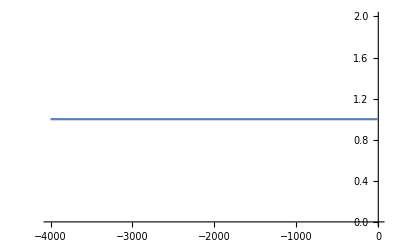

```mathematica
Plot[a11[η]/.sol,{η,start,stop}]
```

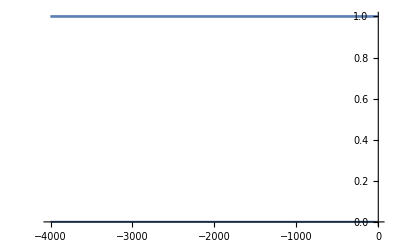

```mathematica
Plot[{Abs[a11[η]],Abs[b11[η]], Abs[a11[η]]^2+Abs[b11[η]]^2}/.sol,{η,start,stop}]
```

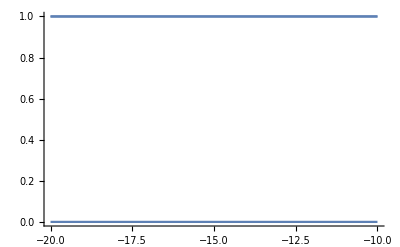

```mathematica
Plot[{Abs[a22[η]],Abs[b22[η]], Abs[a22[η]]^2+Abs[b22[η]]^2}/.sol,{η,-20,stop}]
```

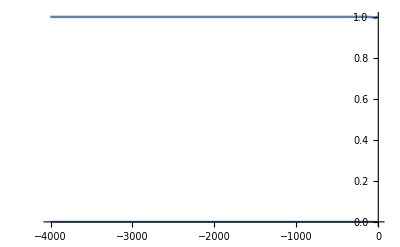

```mathematica
Plot[{Abs[a33[η]],Abs[b33[η]], Abs[a33[η]]^2+Abs[b33[η]]^2}/.sol,{η,start,stop}]
```

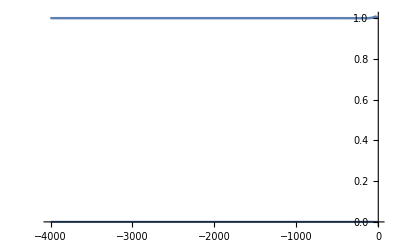

```mathematica
Plot[{Abs[a44[η]],Abs[b44[η]], Abs[a44[η]]^2+Abs[b44[η]]^2}/.sol,{η,start,stop}]
```

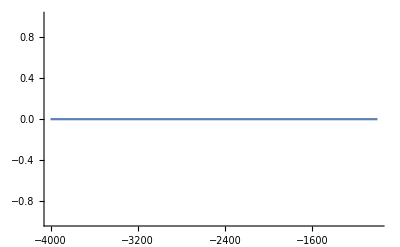

```mathematica
Plot[{Abs[a34[η]]}/.sol,{η,start,-1000}]
```

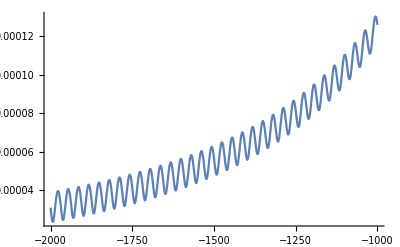

```mathematica
Plot[{Abs[b34[η]]}/.sol,{η,-2000,-1000}]
```

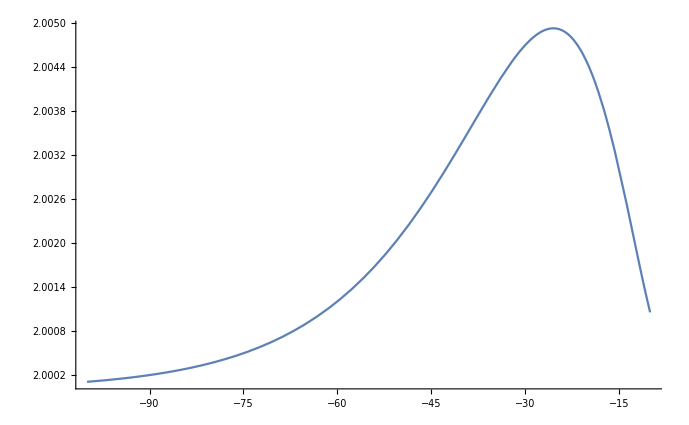

```mathematica
Plot[{Abs[a33[η]]^2+ Abs[a34[η]]^2+ Abs[a43[η]]^2+ Abs[a44[η]]^2+Abs[b33[η]]^2+Abs[b34[η]]^2+Abs[b43[η]]^2+Abs[b44[η]]^2}/.sol,{η,-100,stop}]
```

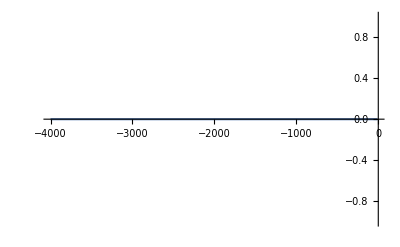
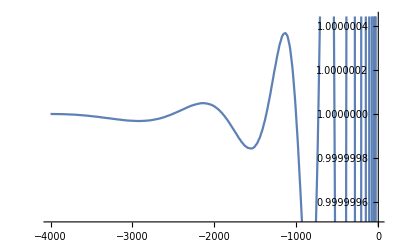
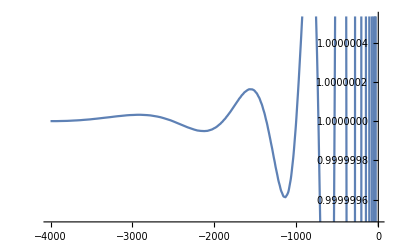
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Table[Plot[Abs[(a[η][[i]][[j]])^2]/.noMsol,{η,start,stop}],{i,1,4},{j,1,4}]
```

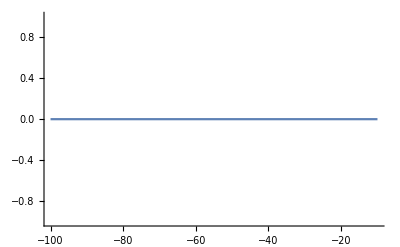
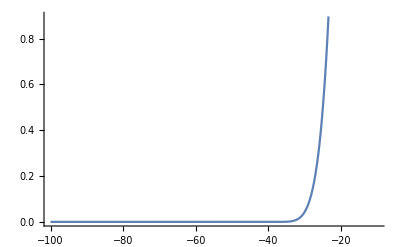
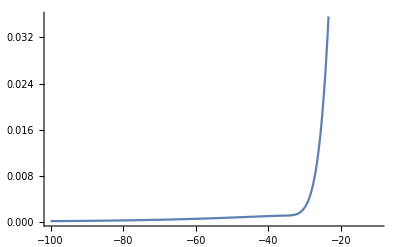
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Table[Plot[Abs[(b[η][[i]][[j]])^2]/.noMsol,{η,-100,-10}],{i,1,4},{j,1,4}]
```

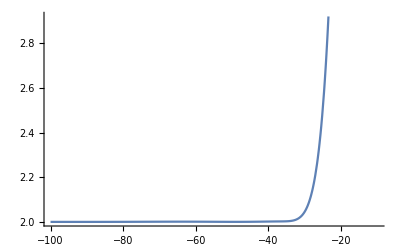

```mathematica
Plot[Abs[a33[η]]^2+Abs[a44[η]]^2+Abs[a43[η]]^2+Abs[a34[η]]^2+Abs[b33[η]]^2+Abs[b44[η]]^2+Abs[b34[η]]^2+Abs[b43[η]]^2/.noMsol,{η,-100,-10}]
```

### No-mass check

```mathematica
M1=0;
M[η_]=-M1/η;
f1=5;
f[η_]=-f1/η; (*Make it picewise*)noMsol[k_] = NDSolve[{a'[η]==a[η].A1[η] + Transpose[ExpPhPlus[η]*Transpose[b[η].B1[η]]], b'[η]== Transpose[ExpPhMinus[η]*Transpose[a[η].A2[η]]]+ b[η].B2[η], Ph1'[η]==fωD[η][[2]],Ph2'[η]==fωD[η][[4]],Ph3'[η]==fωD[η][[6]],Ph4'[η]==fωD[η][[8]], a[start]=={{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}, b[start]=={{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}, Ph1[start]==0,Ph2[start]==0,Ph3[start]==0,Ph4[start]==0},{a11[η],a12[η],a13[η],a14[η],a21[η],a22[η],a23[η],a24[η],a31[η],a32[η],a33[η],a34[η],a41[η],a42[η],a43[η],a44[η],b11[η],b12[η],b13[η],b14[η],b21[η],b22[η],b23[η],b24[η],b31[η],b32[η],b33[η],b34[η],b41[η],b42[η],b43[η],b44[η],Ph1[η],Ph2[η],Ph3[η],Ph4[η]},{η,start,stop}];
```

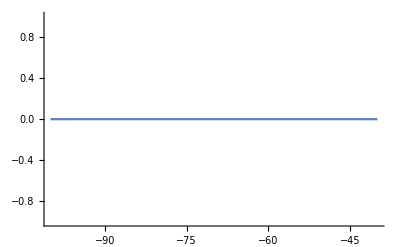
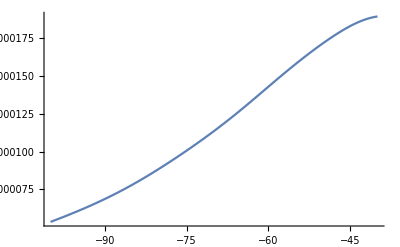
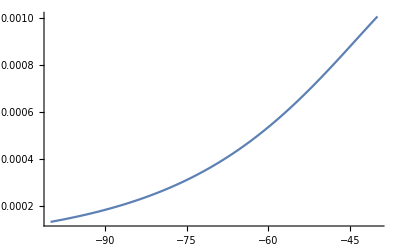
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Table[Plot[Abs[(b[η][[i]][[j]])^2]/.noMsol,{η,-100,stop}],{i,1,4},{j,1,4}]
```

# Weyl basis

#### Matrices definition

```mathematica
γW = {ArrayFlatten[{{0,σto[[1]]},{σto[[1]],0}}],ArrayFlatten[{{0,σto[[2]]},{-σto[[2]],0}}],ArrayFlatten[{{0,σto[[3]]},{-σto[[3]],0}}],ArrayFlatten[{{0,σto[[4]]},{-σto[[4]],0}}]};
```

#### Finding Eigenvalues[] and EigenVectors[]

```mathematica
DiracHamiltonianW=-γW[[1]].γW[[4]]*k+f[η]/2(Sum[γW[[1]].γW[[i]].τ[[i]],{i,2,4}])-M[η]*γW[[1]];
AnsW=FullSimplify[Eigensystem[DiracHamiltonianW]];
```

```mathematica
ωW = Table[AnsW[[1]][[i]],{i,1,8}];
uW = Table[(AnsW[[2]][[i]])/Norm[AnsW[[2]][[i]]],{i,1,8}];
uW[[1]]/.√((-2 k+f[η])^2+4 M[η]^2) -> 2ω1 /.-2 k+f[η]-> sgn[2 k+f[η]]*2*√(ω1^2-M[η]^2)
```

```mathematica
{(2 ω1+2 √(ω1^2-M[η]^2) sgn[2 k+f[η]])/(2 √(1+1/4 Abs[(2 ω1+2 √(ω1^2-M[η]^2) sgn[2 k+f[η]])/M[η]]^2) M[η]),0,0,0,1/(√(1+1/4 Abs[(2 ω1+2 √(ω1^2-M[η]^2) sgn[2 k+f[η]])/M[η]]^2)),0,0,0}
```

```mathematica
(* check scalar product *)
errors =0;
For[i=1,i<=8,i++,
  For[j=1,j<=8,j++,
    product = FullSimplify[Dot[uD[[i]],uD[[j]]]];
    If[i==j && (product===0) , errors++];
    If[i!=j && !(product===0) , errors++];
  ]
]
Print[errors];
```

Part::partd: Part specification uD⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

56

#### derivatives of eigenvectors

```mathematica
duW= Table[D[uW[[i]],η],{i,1,8}];
```

#### scalar product of eigenvectors and its derivatives

```mathematica
productsW=Table[Dot[uW[[i]],duW[[j]]],{i,1,8},{j,1,8}];
productsW//MatrixForm;
```

```mathematica
(* check that up up and down down do not mix  *)  
errors =0;
For[i=3,i<=4,i++,
  For[j=1,j<=2,j++,
    If[(productsW===0) , errors++];  
  ]
]
For[i=1,i<=2,i++,
  For[j=3,j<=4,j++,
    If[(productsW===0) , errors++];  
  ]
]
For[i=5,i<=8,i++,
  For[j=1,j<=4,j++,
    If[(productsW===0) , errors++];  
  ]
]
For[i=1,i<=4,i++,
  For[j=5,j<=8,j++,
    If[(productsW===0) , errors++];  
  ]
]
Print[errors];
```

0

```mathematica
productsW1 = Table[FullSimplify[productsW[[i]][[j]]],{i,1,2},{j,1,2}];
```

```mathematica
productsW2 = Table[FullSimplify[productsW[[i]][[j]]],{i,3,4},{j,3,4}];
```

$Aborted

```mathematica
productsW3 = Table[FullSimplify[productsW[[i]][[j]]],{i,5,8},{j,5,8}];
productsW1
```

```mathematica
productsW1 /.√((-2 k+f[η])^2+4 M[η]^2)->ω1 /.(-2 k+f[η])^2+4 M[η]^2->ω1^2//MatrixForm
```

```mathematica
({{((-2 k+ω1+f[η]) ((4+Abs[(-2 k+ω1+f[η])/M[η]]^2) (-2 k+ω1+f[η]) M[η]+2 Abs[(-2 k+ω1+f[η])/M[η]] (2 k-f[η]) (-2 k+ω1+f[η]) Abs'[(-2 k+ω1+f[η])/M[η]]-8 Abs[(-2 k+ω1+f[η])/M[η]] M[η]^2 Abs'[(-2 k+ω1+f[η])/M[η]]) (M[η] f'[η]+(2 k-f[η]) M'[η]))/(√(ω1^2) (4+Abs[(-2 k+ω1+f[η])/M[η]]^2)^2 M[η]^4), (4 (M[η] f'[η]+(2 k-f[η]) M'[η]))/(√(ω1^2 (4+Abs[(-2 k-ω1+f[η])/M[η]]^2) (4+Abs[(-2 k+ω1+f[η])/M[η]]^2)) M[η])}, {(-4 M[η] f'[η]+4 (-2 k+f[η]) M'[η])/(√(ω1^2 (4+Abs[(-2 k-ω1+f[η])/M[η]]^2) (4+Abs[(-2 k+ω1+f[η])/M[η]]^2)) M[η]), -((2 k+ω1-f[η]) ((4+Abs[(2 k+ω1-f[η])^2/M[η]^2]) (2 k+ω1-f[η]) M[η]+2 Abs[(2 k+ω1-f[η])/M[η]] (2 k-f[η]) (2 k+ω1-f[η]) Abs'[(-2 k-ω1+f[η])/M[η]]+8 Abs[(2 k+ω1-f[η])/M[η]] M[η]^2 Abs'[(-2 k-ω1+f[η])/M[η]]) (M[η] f'[η]+(2 k-f[η]) M'[η]))/(√(ω1^2) (4+Abs[(2 k+ω1-f[η])^2/M[η]^2])^2 M[η]^4)}})
```

## blabla

```mathematica
Ηf=-1;
ΗM=-9;
cf=1;
cη=1;
cM1=1;
cM2=10;
f[η_]:=Piecewise[{{-cη/Ηf,η<=Ηf},{-cη/η  ,Ηf<η}}];
M[η_]:=Piecewise[{{0,η<=ΗM},{Exp[cM*η+cM2]- Exp[cM*ΗM+cM2],ΗM<η}}]
```

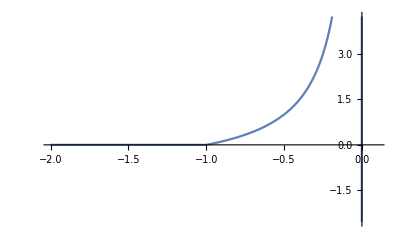

```mathematica
Plot[f[η],{η,-2,0.1}]
```

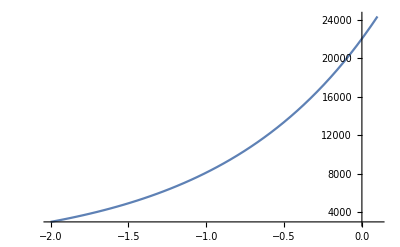

$Aborted

```mathematica
Plot[M[η],{η,-2,0.1}]
```

```mathematica
Sign[-3]
```

-1

$Aborted

```mathematica
1/(√(ω3-M[η]) √(ω3+M[η]))(-(2 f[η] (3 (f[η]^2)^(3/2) √(k^2+f[η]^2)+k^2 (6 √(f[η]^2) √(k^2+f[η]^2)-2 √(f[η]^2 (k^2+f[η]^2)))) (ω3-M[η]) (ω3+M[η]) f'[η])/(√(k^2+f[η]^2) (4 k^2+3 f[η]^2))+(2 (-k^2 √(f[η]^2)+√(k^2+f[η]^2) √(f[η]^2 (k^2+f[η]^2))) (ω3^2-M[η]^2) f'[η])/f[η]+1/(√((ω3^2-M[η]^2)/(k^2+f[η]^2)))(4 k^2 ω3 √(ω3-M[η]) √(ω3+M[η])+(4 k^2 ω3 √(k^2+f[η]^2)-ω3 √(f[η]^2) √(f[η]^2 (k^2+f[η]^2))+2 (√(f[η]^2) (k^2+f[η]^2)-√(k^2+f[η]^2) √(f[η]^2 (k^2+f[η]^2))) M[η]) √((ω3^2-M[η]^2)/(k^2+f[η]^2))+ω3 f[η]^2 (3 √(ω3-M[η]) √(ω3+M[η])+4 √(k^2+f[η]^2) √((ω3^2-M[η]^2)/(k^2+f[η]^2)))) M'[η])==0
```

```mathematica
Assuming[f[η]>0 && k >0&&M[η]>0,FullSimplify[1/4 √(-k f[η]+√(f[η]^2 (k^2+f[η]^2))) (((2 k+3 f[η]) √(-√(f[η]^2)+2 √(k^2+f[η]^2)) √(2 M[η]+√(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2))))/(√(-f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))))-(√(√(f[η]^2)+2 √(k^2+f[η]^2)) √(-2 M[η]+√(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2))) (2 M[η]+√(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2))))/(√(f[η]^2+2 √(f[η]^2 (k^2+f[η]^2)))))==0]]
```

```mathematica
(√f[η] (2 k+3 f[η])-√(f[η] (4 k^2+5 f[η]^2+4 f[η] √(k^2+f[η]^2)))) √(f[η] (-k+√(k^2+f[η]^2)) (2 M[η]+√(5 f[η]^2+4 f[η] √(k^2+f[η]^2)+4 (k^2+M[η]^2))))==0
```

```mathematica
FullSimplify[4 M[η]^2==5 f[η]^2+4 f[η] √(k^2+f[η]^2)+4 (k^2+M[η]^2)]
```

```mathematica
4 k^2+5 f[η]^2+4 f[η] √(k^2+f[η]^2)==0
```

```mathematica
FullSimplify[(√f[η] (2 k+3 f[η]))^2==f[η] (4 k^2+5 f[η]^2+4 f[η] √(k^2+f[η]^2))];
FullSimplify[f[η]^2 (3 k+f[η])^2==k^2+f[η]^2]
```

```mathematica
f[η]^2 (3 k+f[η])^2==k^2+f[η]^2
```

```mathematica
FullSimplify[(2 M[η])^2==5 f[η]^2+4 f[η] √(k^2+f[η]^2)+4 (k^2+M[η]^2)]
```

```mathematica
4 k^2+5 f[η]^2+4 f[η] √(k^2+f[η]^2)==0
```

```mathematica
Full
```

```mathematica
Assuming[f[η]>0 && k >0&&M[η]>0,FullSimplify[DiracHamiltonianD.suD[[8]]==ωD[[8]]*suD[[8]]]]
```

```mathematica
{0,(√(-k+√(k^2+f[η]^2)) (-2 √(ω4-M[η]) M[η]+(2 k+3 f[η]) √(ω4+M[η]))-√((-k+√(k^2+f[η]^2)) (ω4-M[η]) (5 f[η]^2+4 f[η] √(k^2+f[η]^2)+4 (k^2+M[η]^2))))/(2 √2),(√(-k+√(k^2+f[η]^2)) (2 √(ω4-M[η]) M[η]+(2 k-3 f[η]) √(ω4+M[η]))+√((-k+√(k^2+f[η]^2)) (ω4-M[η]) (5 f[η]^2+4 f[η] √(k^2+f[η]^2)+4 (k^2+M[η]^2))))/(2 √2),0,0,(-2 k √((-k+√(k^2+f[η]^2)) (ω4-M[η]))-3 f[η] √((-k+√(k^2+f[η]^2)) (ω4-M[η]))-2 M[η] √((-k+√(k^2+f[η]^2)) (ω4+M[η]))+√((-k+√(k^2+f[η]^2)) (ω4+M[η]) (5 f[η]^2+4 f[η] √(k^2+f[η]^2)+4 (k^2+M[η]^2))))/(2 √2),-(2 k √((-k+√(k^2+f[η]^2)) (ω4-M[η]))-3 f[η] √((-k+√(k^2+f[η]^2)) (ω4-M[η]))-2 M[η] √((-k+√(k^2+f[η]^2)) (ω4+M[η]))+√((-k+√(k^2+f[η]^2)) (ω4+M[η]) (5 f[η]^2+4 f[η] √(k^2+f[η]^2)+4 (k^2+M[η]^2))))/(2 √2),0}=={0,0,0,0,0,0,0,0}
```

```mathematica
Assuming[f[η]>0 && k >0&&M[η]>0 && ω4 > M[η],FullSimplify[(√(-k+√(k^2+f[η]^2)) (-2 √(ω4-M[η]) M[η]+(2 k+3 f[η]) √(ω4+M[η])))^2==(-k+√(k^2+f[η]^2)) (ω4-M[η]) (5 f[η]^2+4 f[η] √(k^2+f[η]^2)+4 (k^2+M[η]^2))]]
```

```mathematica
4 k M[η] (-k+√(ω4^2-M[η]^2))+2 f[η] (ω4 (-3 k+√(k^2+f[η]^2))-M[η] (3 k+√(k^2+f[η]^2)-3 √(ω4^2-M[η]^2)))==f[η]^2 (2 ω4+7 M[η])
```

```mathematica
Assuming[f[η]>0 && k >0&&M[η]>0 && ω4 > M[η],FullSimplify[4 k M[η] (-k+√(ω4^2-M[η]^2))+2 f[η] (ω4 (-3 k+√(k^2+f[η]^2))-M[η] (3 k+√(k^2+f[η]^2)-3 √(ω4^2-M[η]^2)))==f[η]^2 (2 ω4+7 M[η])/.ω4 -> ωD[[8]]]]
```

```mathematica
(-7 f[η]^2+2 k (-2 k+√(4 k^2+5 f[η]^2+4 f[η] √(k^2+f[η]^2)))+f[η] (-6 k-2 √(k^2+f[η]^2)+3 √(4 k^2+5 f[η]^2+4 f[η] √(k^2+f[η]^2)))) M[η]+f[η] (-3 k-f[η]+√(k^2+f[η]^2)) √(5 f[η]^2+4 f[η] √(k^2+f[η]^2)+4 (k^2+M[η]^2))==0
```

```mathematica
Assuming[f[η]>0 && k >0&&M[η]>0 && ω4 > M[η],FullSimplify[((-7 f[η]^2+2 k (-2 k+√(4 k^2+5 f[η]^2+4 f[η] √(k^2+f[η]^2)))+f[η] (-6 k-2 √(k^2+f[η]^2)+3 √(4 k^2+5 f[η]^2+4 f[η] √(k^2+f[η]^2)))) M[η])^2==(f[η] (-3 k-f[η]+√(k^2+f[η]^2)) √(5 f[η]^2+4 f[η] √(k^2+f[η]^2)+4 (k^2+M[η]^2)))^2]]
```

```mathematica
(-7 f[η]^2+2 k (-2 k+√(4 k^2+5 f[η]^2+4 f[η] √(k^2+f[η]^2)))+f[η] (-6 k-2 √(k^2+f[η]^2)+3 √(4 k^2+5 f[η]^2+4 f[η] √(k^2+f[η]^2))))^2 M[η]^2==f[η]^2 (3 k+f[η]-√(k^2+f[η]^2))^2 (5 f[η]^2+4 f[η] √(k^2+f[η]^2)+4 (k^2+M[η]^2))
```

```mathematica
Assuming[f[η]>0 && k >0&&M[η]>0 ,FullSimplify[(-7 f[η]^2+2 k (-2 k+√(4 k^2+5 f[η]^2+4 f[η] √(k^2+f[η]^2)))+f[η] (-6 k-2 √(k^2+f[η]^2)+3 √(4 k^2+5 f[η]^2+4 f[η] √(k^2+f[η]^2))))^2==4*f[η]^2 (3 k+f[η]-√(k^2+f[η]^2))^2 ]]
```

False

```mathematica
Assuming[f[η]>0 && k >0&&M[η]>0 && ω[η]>M[η],FullSimplify[DiracHamiltonianD.suD[[6]]==ωD[[6]]*suD[[6]]]]
```

```mathematica
{0,-1/(2 √2)(2 √((-k+√(k^2+f[η]^2)) (ω3-M[η])) M[η]+2 k √((-k+√(k^2+f[η]^2)) (ω3+M[η]))+f[η] √((-k+√(k^2+f[η]^2)) (ω3+M[η]))-2 f[η] √((k+√(k^2+f[η]^2)) (ω3+M[η]))+√(-((-k+√(k^2+f[η]^2)) (ω3-M[η]) (-5 f[η]^2+4 f[η] √(k^2+f[η]^2)-4 (k^2+M[η]^2))))),-1/(2 √2)(2 √((k+√(k^2+f[η]^2)) (ω3-M[η])) M[η]-2 f[η] √((-k+√(k^2+f[η]^2)) (ω3+M[η]))-2 k √((k+√(k^2+f[η]^2)) (ω3+M[η]))+f[η] √((k+√(k^2+f[η]^2)) (ω3+M[η]))+√(-((k+√(k^2+f[η]^2)) (ω3-M[η]) (-5 f[η]^2+4 f[η] √(k^2+f[η]^2)-4 (k^2+M[η]^2))))),0,0,-1/(2 √2)(2 k √((-k+√(k^2+f[η]^2)) (ω3-M[η]))+f[η] √((-k+√(k^2+f[η]^2)) (ω3-M[η]))-2 f[η] √((k+√(k^2+f[η]^2)) (ω3-M[η]))-2 M[η] √((-k+√(k^2+f[η]^2)) (ω3+M[η]))+√((-k+√(k^2+f[η]^2)) (ω3+M[η]) (5 f[η]^2-4 f[η] √(k^2+f[η]^2)+4 (k^2+M[η]^2)))),-1/(2 √2)(-2 f[η] √((-k+√(k^2+f[η]^2)) (ω3-M[η]))-2 k √((k+√(k^2+f[η]^2)) (ω3-M[η]))+f[η] √((k+√(k^2+f[η]^2)) (ω3-M[η]))-2 M[η] √((k+√(k^2+f[η]^2)) (ω3+M[η]))+√((k+√(k^2+f[η]^2)) (ω3+M[η]) (5 f[η]^2-4 f[η] √(k^2+f[η]^2)+4 (k^2+M[η]^2)))),0}=={0,0,0,0,0,0,0,0}
```

```mathematica
Assuming[f[η]>0 && k >0&&M[η]>0 && ω[η]>M[η],FullSimplify[-1/(2 √2)(2 √((-k+√(k^2+f[η]^2)) (ω3-M[η])) M[η]+2 k √((-k+√(k^2+f[η]^2)) (ω3+M[η]))+f[η] √((-k+√(k^2+f[η]^2)) (ω3+M[η]))-2 f[η] √((k+√(k^2+f[η]^2)) (ω3+M[η]))+√(-((-k+√(k^2+f[η]^2)) (ω3-M[η]) (-5 f[η]^2+4 f[η] √(k^2+f[η]^2)-4 (k^2+M[η]^2)))))==0/.ω3 -> ωD[[6]]]]
```

```mathematica
2 M[η] √((-k+√(k^2+f[η]^2)) (-2 M[η]+√(5 f[η]^2-4 f[η] √(k^2+f[η]^2)+4 (k^2+M[η]^2))))+√(-((-k+√(k^2+f[η]^2)) (-5 f[η]^2+4 f[η] √(k^2+f[η]^2)-4 (k^2+M[η]^2)) (-2 M[η]+√(5 f[η]^2-4 f[η] √(k^2+f[η]^2)+4 (k^2+M[η]^2)))))+2 k √((-k+√(k^2+f[η]^2)) (2 M[η]+√(5 f[η]^2-4 f[η] √(k^2+f[η]^2)+4 (k^2+M[η]^2))))+f[η] √((-k+√(k^2+f[η]^2)) (2 M[η]+√(5 f[η]^2-4 f[η] √(k^2+f[η]^2)+4 (k^2+M[η]^2))))==2 f[η] √((k+√(k^2+f[η]^2)) (2 M[η]+√(5 f[η]^2-4 f[η] √(k^2+f[η]^2)+4 (k^2+M[η]^2))))
```

```mathematica
suD[[8]]
```

```mathematica
{0,(√(1/2 √(f[η]^2)+√(k^2+f[η]^2)) √(-k f[η]+√(f[η]^2 (k^2+f[η]^2))) √(ω4-M[η]))/(√(f[η]^2+2 √(f[η]^2 (k^2+f[η]^2)))),-(√(1/2 √(f[η]^2)+√(k^2+f[η]^2)) √(-k f[η]+√(f[η]^2 (k^2+f[η]^2))) √(ω4-M[η]))/(√(f[η]^2+2 √(f[η]^2 (k^2+f[η]^2)))),0,0,-(√(-1/2 √(f[η]^2)+√(k^2+f[η]^2)) √(-k f[η]+√(f[η]^2 (k^2+f[η]^2))) √(ω4+M[η]))/(√(-f[η]^2+2 √(f[η]^2 (k^2+f[η]^2)))),(√(-1/2 √(f[η]^2)+√(k^2+f[η]^2)) √(-k f[η]+√(f[η]^2 (k^2+f[η]^2))) √(ω4+M[η]))/(√(-f[η]^2+2 √(f[η]^2 (k^2+f[η]^2)))),0}
```

```mathematica
uD[[8]]
```

```mathematica
{0,((k f[η]+√(f[η]^2 (k^2+f[η]^2))) (-2 M[η]+√(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2))))/(f[η]^3+2 f[η] √(f[η]^2 (k^2+f[η]^2))),-(f[η] (-2 M[η]+√(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2))))/(f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))),0,0,-(k f[η]+√(f[η]^2 (k^2+f[η]^2)))/f[η]^2,1,0}
```

```mathematica
Assuming[f[η]>0 && k >0&&M[η]>0 ,FullSimplify[(√(-1/2 √(f[η]^2)+√(k^2+f[η]^2)) √(-k f[η]+√(f[η]^2 (k^2+f[η]^2))) √(ω4+M[η]))/(√(-f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))))*uD[[8]]==suD[[8]]/.ω4->ωD[[8]]]]
```

```mathematica
{0,-1/2 √((-k+√(k^2+f[η]^2)) (-2 M[η]+√(f[η] (5 f[η]+4 √(k^2+f[η]^2))+4 (k^2+M[η]^2))))+((k+√(k^2+f[η]^2)) (-2 M[η]+√(f[η] (5 f[η]+4 √(k^2+f[η]^2))+4 (k^2+M[η]^2))) √((-k+√(k^2+f[η]^2)) (2 M[η]+√(f[η] (5 f[η]+4 √(k^2+f[η]^2))+4 (k^2+M[η]^2)))))/(2 f[η] (f[η]+2 √(k^2+f[η]^2))),1/2 √((-k+√(k^2+f[η]^2)) (-2 M[η]+√(5 f[η]^2+4 f[η] √(k^2+f[η]^2)+4 (k^2+M[η]^2))))-((-2 M[η]+√(5 f[η]^2+4 f[η] √(k^2+f[η]^2)+4 (k^2+M[η]^2))) √((-k+√(k^2+f[η]^2)) (2 M[η]+√(5 f[η]^2+4 f[η] √(k^2+f[η]^2)+4 (k^2+M[η]^2)))))/(2 (f[η]+2 √(k^2+f[η]^2))),0,0,-((k-f[η]+√(k^2+f[η]^2)) √((-k+√(k^2+f[η]^2)) (2 M[η]+√(5 f[η]^2+4 f[η] √(k^2+f[η]^2)+4 (k^2+M[η]^2)))))/(2 f[η]),0,0}=={0,0,0,0,0,0,0,0}
```

```mathematica
Assuming[f[η]>0 && k >0&&M[η]>0 ,FullSimplify[(2 M[η])^2==5 f[η]^2+4 f[η] √(k^2+f[η]^2)+4 (k^2+M[η]^2)]]
```

False

```mathematica
uD[[1]]
```

```mathematica
{(2 M[η]+√((-2 k+f[η])^2+4 M[η]^2))/(2 k-f[η]),0,0,0,1,0,0,0}
```

```mathematica
suD[[1]]
```

```mathematica
{(√(ω1+M[η]))/Sign[2 k-f[η]],0,0,0,√(ω1-M[η]),0,0,0}
```

```mathematica
Norm[suD[[1]]]
```

```mathematica
√(Abs[ω1-M[η]]+Abs[(√(ω1+M[η]))/Sign[2 k-f[η]]]^2)
```

```mathematica
Assuming[f[η]>0 && k >0&&M[η]>0 ,FullSimplify[√(ω1-M[η])*uD[[1]]==suD[[1]]/.ω1 -> ωD[[2]]]]
```

True

```mathematica
Assuming[f[η]>0 && k >0&&M[η]>0 ,FullSimplify[√(ω1+M[η])*uD[[2]]==suD[[2]]/.ω1 -> ωD[[2]]]]
```

True

```mathematica
Assuming[f[η]>0 && k >0&&M[η]>0 ,FullSimplify[√(ω2-M[η])*uD[[3]]==suD[[3]]/.ω2 -> ωD[[4]]]]
```

True

```mathematica
Assuming[f[η]>0 && k >0&&M[η]>0 ,FullSimplify[√(ω2+M[η])*uD[[4]]==suD[[4]]/.ω2 -> ωD[[4]]] ]
```

True

```mathematica
uD[[5]]
```

```mathematica
{0,((-k f[η]+√(f[η]^2 (k^2+f[η]^2))) (2 M[η]+√(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))))/(f[η]^3-2 f[η] √(f[η]^2 (k^2+f[η]^2))),(f[η] (2 M[η]+√(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))))/(f[η]^2-2 √(f[η]^2 (k^2+f[η]^2))),0,0,(-k f[η]+√(f[η]^2 (k^2+f[η]^2)))/f[η]^2,1,0}
```

```mathematica
suD[[5]]
```

```mathematica
{0,-(√(-1/2 √(f[η]^2)+√(k^2+f[η]^2)) √(-k f[η]+√(f[η]^2 (k^2+f[η]^2))) √(ω3+M[η]))/(√(-f[η]^2+2 √(f[η]^2 (k^2+f[η]^2)))),-(√(-1/2 √(f[η]^2)+√(k^2+f[η]^2)) √(k f[η]+√(f[η]^2 (k^2+f[η]^2))) √(ω3+M[η]))/(√(-f[η]^2+2 √(f[η]^2 (k^2+f[η]^2)))),0,0,(√(1/2 √(f[η]^2)+√(k^2+f[η]^2)) √(-k f[η]+√(f[η]^2 (k^2+f[η]^2))) √(ω3-M[η]))/(√(f[η]^2+2 √(f[η]^2 (k^2+f[η]^2)))),(√(1/2 √(f[η]^2)+√(k^2+f[η]^2)) √(k f[η]+√(f[η]^2 (k^2+f[η]^2))) √(ω3-M[η]))/(√(f[η]^2+2 √(f[η]^2 (k^2+f[η]^2)))),0}
```

```mathematica
Assuming[f[η]>0 && k >0&&M[η]>0 ,FullSimplify[(√(1/2 √(f[η]^2)+√(k^2+f[η]^2)) √(k f[η]+√(f[η]^2 (k^2+f[η]^2))) √(ω3-M[η]))/(√(f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))))*uD[[5]]==suD[[5]]/.ω3 -> ωD[[6]]] ]
```

```mathematica
{0,((-k+√(k^2+f[η]^2)) √((k+√(k^2+f[η]^2)) (-2 M[η]+√(f[η] (5 f[η]-4 √(k^2+f[η]^2))+4 (k^2+M[η]^2)))) (2 M[η]+√(f[η] (5 f[η]-4 √(k^2+f[η]^2))+4 (k^2+M[η]^2))))/(2 f[η] (f[η]-2 √(k^2+f[η]^2)))+1/2 √((-k+√(k^2+f[η]^2)) (2 M[η]+√(f[η] (5 f[η]-4 √(k^2+f[η]^2))+4 (k^2+M[η]^2)))),(√((k+√(k^2+f[η]^2)) (-2 M[η]+√(5 f[η]^2-4 f[η] √(k^2+f[η]^2)+4 (k^2+M[η]^2)))) (2 M[η]+√(5 f[η]^2-4 f[η] √(k^2+f[η]^2)+4 (k^2+M[η]^2))))/(2 (f[η]-2 √(k^2+f[η]^2)))+1/2 √((k+√(k^2+f[η]^2)) (2 M[η]+√(5 f[η]^2-4 f[η] √(k^2+f[η]^2)+4 (k^2+M[η]^2)))),0,0,-1/2 √((-k+√(k^2+f[η]^2)) (-2 M[η]+√(f[η] (5 f[η]-4 √(k^2+f[η]^2))+4 (k^2+M[η]^2))))+1/2 f[η] (-k+√(k^2+f[η]^2)) √(((k+√(k^2+f[η]^2)) (-2 M[η]+√(f[η] (5 f[η]-4 √(k^2+f[η]^2))+4 (k^2+M[η]^2))))/f[η]^4),0,0}=={0,0,0,0,0,0,0,0}
```

```mathematica
suD[[5]]
```

```mathematica
{0,-(√(-1/2 √(f[η]^2)+√(k^2+f[η]^2)) √(-k f[η]+√(f[η]^2 (k^2+f[η]^2))) √(ω3+M[η]))/(√(-f[η]^2+2 √(f[η]^2 (k^2+f[η]^2)))),-(√(-1/2 √(f[η]^2)+√(k^2+f[η]^2)) √(k f[η]+√(f[η]^2 (k^2+f[η]^2))) √(ω3+M[η]))/(√(-f[η]^2+2 √(f[η]^2 (k^2+f[η]^2)))),0,0,(√(1/2 √(f[η]^2)+√(k^2+f[η]^2)) √(-k f[η]+√(f[η]^2 (k^2+f[η]^2))) √(ω3-M[η]))/(√(f[η]^2+2 √(f[η]^2 (k^2+f[η]^2)))),(√(1/2 √(f[η]^2)+√(k^2+f[η]^2)) √(k f[η]+√(f[η]^2 (k^2+f[η]^2))) √(ω3-M[η]))/(√(f[η]^2+2 √(f[η]^2 (k^2+f[η]^2)))),0}
uD[[5]]
```

```mathematica
{0,-(√(-1/2 √(f[η]^2)+√(k^2+f[η]^2)) √(-k f[η]+√(f[η]^2 (k^2+f[η]^2))) √(ω3+M[η]))/(√(-f[η]^2+2 √(f[η]^2 (k^2+f[η]^2)))),-(√(-1/2 √(f[η]^2)+√(k^2+f[η]^2)) √(k f[η]+√(f[η]^2 (k^2+f[η]^2))) √(ω3+M[η]))/(√(-f[η]^2+2 √(f[η]^2 (k^2+f[η]^2)))),0,0,(√(1/2 √(f[η]^2)+√(k^2+f[η]^2)) √(-k f[η]+√(f[η]^2 (k^2+f[η]^2))) √(ω3-M[η]))/(√(f[η]^2+2 √(f[η]^2 (k^2+f[η]^2)))),(√(1/2 √(f[η]^2)+√(k^2+f[η]^2)) √(k f[η]+√(f[η]^2 (k^2+f[η]^2))) √(ω3-M[η]))/(√(f[η]^2+2 √(f[η]^2 (k^2+f[η]^2)))),0}
```

```mathematica
{0,((-k f[η]+√(f[η]^2 (k^2+f[η]^2))) (2 M[η]+√(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))))/(f[η]^3-2 f[η] √(f[η]^2 (k^2+f[η]^2))),(f[η] (2 M[η]+√(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))))/(f[η]^2-2 √(f[η]^2 (k^2+f[η]^2))),0,0,(-k f[η]+√(f[η]^2 (k^2+f[η]^2)))/f[η]^2,1,0}
```

```mathematica
ssuD5=(√(1/2 √(f[η]^2)+√(k^2+f[η]^2)) √(k f[η]+√(f[η]^2 (k^2+f[η]^2))) √(ω3-M[η]))/(√(f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))))uD[[5]]
```

```mathematica
{0,(√(1/2 √(f[η]^2)+√(k^2+f[η]^2)) (-k f[η]+√(f[η]^2 (k^2+f[η]^2))) √(k f[η]+√(f[η]^2 (k^2+f[η]^2))) √(ω3-M[η]) (2 M[η]+√(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))))/(√(f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))) (f[η]^3-2 f[η] √(f[η]^2 (k^2+f[η]^2)))),(f[η] √(1/2 √(f[η]^2)+√(k^2+f[η]^2)) √(k f[η]+√(f[η]^2 (k^2+f[η]^2))) √(ω3-M[η]) (2 M[η]+√(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))))/((f[η]^2-2 √(f[η]^2 (k^2+f[η]^2))) √(f[η]^2+2 √(f[η]^2 (k^2+f[η]^2)))),0,0,(√(1/2 √(f[η]^2)+√(k^2+f[η]^2)) (-k f[η]+√(f[η]^2 (k^2+f[η]^2))) √(k f[η]+√(f[η]^2 (k^2+f[η]^2))) √(ω3-M[η]))/(f[η]^2 √(f[η]^2+2 √(f[η]^2 (k^2+f[η]^2)))),(√(1/2 √(f[η]^2)+√(k^2+f[η]^2)) √(k f[η]+√(f[η]^2 (k^2+f[η]^2))) √(ω3-M[η]))/(√(f[η]^2+2 √(f[η]^2 (k^2+f[η]^2)))),0}
```

```mathematica
Assuming[f[η]>0 && k >0&&M[η]>0,FullSimplify[ssuD5[[6]]/suD[[5]][[6]]==1]]
```

True

```mathematica
For[i=1, i<=8, i++,
	multiplier =0;
	For[j=1,j<=8,j++,
		multiplier=0;
		If[uD[[i]][[j]]==1,
			multiplier = suD[[i]][[j]];
		];
	];
	muD = multiplier* uD[[i]];
	For[k=1,k<=8,k++,
		If[suD[[i]][[j]]==0 && muD[[j]] != 0,
			Print["Error for: ",i,j]
		]
		If[suD[[i]][[j]]!=0,
			If[! Assuming[f[η]>0 && k >0&&M[η]>0,FullSimplify[muD[[j]]/suD[[i]][[j]]==1]],
				Print["Error for: ",i,j]
			];
		];
	]
]
```

Part::partd: Part specification uD⟦1⟧ is longer than depth of object.

Part::partd: Part specification suD⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 3 of uD⟦1⟧ does not exist.

Part::partw: Part 4 of uD⟦1⟧ does not exist.

Part::partw: Part 5 of uD⟦1⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.